## Numerical Example (Homog. b.c. for u and p):

```mathematica
lambda=1;
mu=1;
alpha=1;
c0=1e-05;
K=perm*IdentityMatrix[2];
perm=1,1e-03,...,1e-12;
```

```mathematica
Clear[lambda,mu,alpha,c0]
```

### Displacement :

```mathematica
u[x_,y_,t_]:=Exp[t]{x^3 y^4+x^2+Sin[(1-x)(1-y)]Cos[1-y],(1-x)^4(1-y)^3+(1-y)^2+Cos[x y]Sin[x]}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{ⅇ^t Cos[1-y] Sin[1-y],ⅇ^t ((1-y)^2+(1-y)^3)}

```mathematica
u[1,y,t]
```

{ⅇ^t (1+y^4),ⅇ^t ((1-y)^2+Cos[y] Sin[1])}

```mathematica
u[x,0,t]
```

{ⅇ^t (x^2+Cos[1] Sin[1-x]),ⅇ^t (1+(1-x)^4+Sin[x])}

```mathematica
u[x,1,t]
```

{ⅇ^t (x^2+x^3),ⅇ^t Cos[x] Sin[x]}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

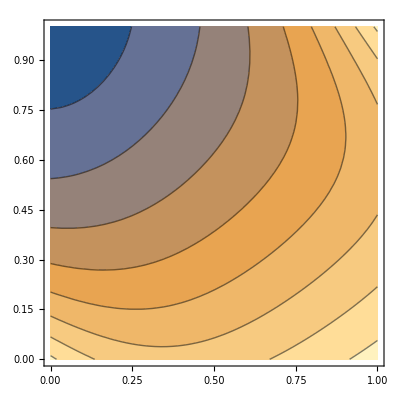

```mathematica
ContourPlot[Sqrt[(Exp[t](x^3 y^4+x^2+Sin[(1-x)(1-y)]Cos[1-y]))^2+(Exp[t]((1-x)^4(1-y)^3+(1-y)^2+Cos[x y]Sin[x]))^2]/.t->0.001,{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_,t_]:=Exp[t](10+Sin[Pi x] Cos[Pi y])
```

```mathematica
p[0,y,t]
```

10 ⅇ^t

```mathematica
p[1,y,t]
```

10 ⅇ^t

```mathematica
p[x,0,t]
```

ⅇ^t (10+Sin[π x])

```mathematica
p[x,1,t]
```

ⅇ^t (10-Sin[π x])

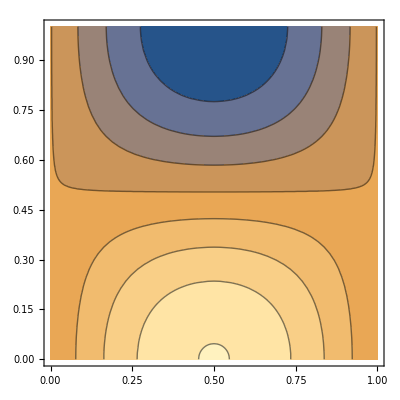

```mathematica
ContourPlot[p[x,y,0.001],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
Gradu[x_,y_,t_]:={{D[u[x,y,t][[1]], x],D[u[x,y,t][[1]], y]},{D[u[x,y,t][[2]], x],D[u[x,y,t][[2]], y]}}
```

Let us define ϵ (u) :

```mathematica
w=1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{ⅇ^t (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]),1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
Sigmae[x_,y_,t_]:=2mu w+lambda Tr[w]IdentityMatrix[2]//Simplify
```

```mathematica
Sigmae[x,y,t]
```

{{ⅇ^t (2 mu (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])),ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (2 mu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))}}

Let us define the stress function as the previous expression :

### Stress:

```mathematica
Sigma[x_,y_,t_]:=Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

```mathematica
Sigma[x,y,t]
```

{{ⅇ^t (2 mu (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)])-alpha (10+Cos[π y] Sin[π x])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])),ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+2 mu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))}}

ContourPlot of the Magnitude of the first row of σ :

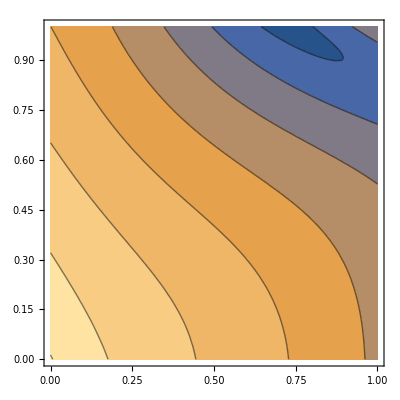

```mathematica
ContourPlot[Sqrt[(ⅇ^t (2 mu (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)])-alpha (10+Cos[π y] Sin[π x])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])))^2+(ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]))^2]/.{lambda->1,mu->1,alpha->1,t->0.001},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

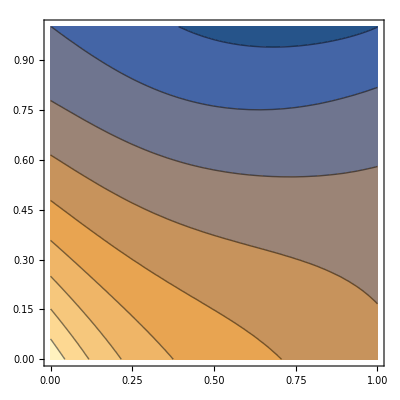

```mathematica
ContourPlot[Sqrt[(ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]))^2+(ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+2 mu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])))^2]/.{lambda->1,mu->1,alpha->1,t->0.001},{x,0,1},{y,0,1}]
```

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,1/2 ⅇ^t (4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]-Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]+y Sin[x] Sin[x y])},{1/2 ⅇ^t (-4 (-1+x)^3 (-1+y)^3-4 x^3 y^3-(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]-Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),0}}

ContourPlot of the element in the first row and second column of the rotation:

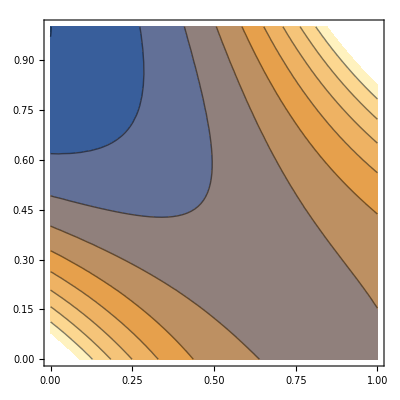

```mathematica
ContourPlot[1/2 ⅇ^t (4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]-Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]+y Sin[x] Sin[x y])/.{lambda->1,mu->1,alpha->1,t->0.001},{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
K = perm*IdentityMatrix[2];
```

```mathematica
-K.{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{-ⅇ^t perm π Cos[π x] Cos[π y],ⅇ^t perm π Sin[π x] Sin[π y]}

```mathematica
z[x_,y_,t_]:={-ⅇ^t perm π Cos[π x] Cos[π y],ⅇ^t perm π Sin[π x] Sin[π y]}
```

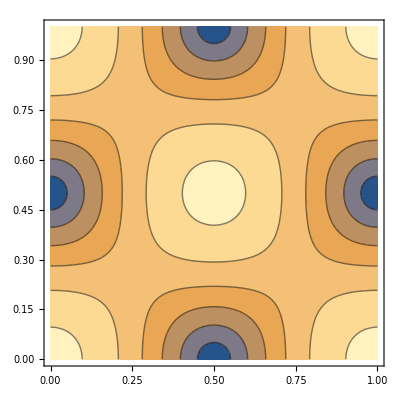

```mathematica
ContourPlot[Sqrt[(-ⅇ^t perm π Cos[π x] Cos[π y])^2+(ⅇ^t perm π Sin[π x] Sin[π y])^2]/.{perm->1,t->0.001},{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{ⅇ^t (2 mu (x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)])-alpha (10+Cos[π y] Sin[π x])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y])),ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y])},{ⅇ^t mu (-4 (-1+x)^3 (-1+y)^3+4 x^3 y^3+(-1+x) Cos[1-y] Cos[(-1+x) (-1+y)]+Cos[x] Cos[x y]+Sin[1-y] Sin[(-1+x) (-1+y)]-y Sin[x] Sin[x y]),ⅇ^t (-alpha (10+Cos[π y] Sin[π x])+2 mu (2 (-1+y)-3 (-1+x)^4 (-1+y)^2-x Sin[x] Sin[x y])+lambda (2 (-1+y)-3 (-1+x)^4 (-1+y)^2+x (2+3 x y^4)+(-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]-x Sin[x] Sin[x y]))}}

```mathematica
f[x_,y_,t_]:={-Div[{Sigma[x,y,t][[1,1]],Sigma[x,y,t][[1,2]]},{x,y}],-Div[{Sigma[x,y,t][[2,1]],Sigma[x,y,t][[2,2]]},{x,y}]}
```

```mathematica
f[x,y,t]//Simplify
```

{ⅇ^t (12 mu (-1+x)^3 (-1+y)^2-12 mu x^3 y^2+alpha π Cos[π x] Cos[π y]+mu x y Cos[x y] Sin[x]-2 mu (-1+x) Cos[(-1+x) (-1+y)] Sin[1-y]+mu Cos[1-y] Sin[(-1+x) (-1+y)]+mu (-1+x)^2 Cos[1-y] Sin[(-1+x) (-1+y)]-2 mu (2+6 x y^4-(-1+y)^2 Cos[1-y] Sin[(-1+x) (-1+y)])+mu x Cos[x] Sin[x y]+mu Sin[x] Sin[x y]-lambda (2-12 (-1+x)^3 (-1+y)^2+6 x y^4-x y Cos[x y] Sin[x]-(-1+y)^2 Cos[1-y] Sin[(-1+x) (-1+y)]-x Cos[x] Sin[x y]-Sin[x] Sin[x y])),ⅇ^t (-2 mu (2-6 (-1+x)^4 (-1+y)-x^2 Cos[x y] Sin[x])-lambda (2-6 (-1+x)^4 (-1+y)+12 x^2 y^3+Cos[1-y] Cos[(-1+x) (-1+y)]-x^2 Cos[x y] Sin[x]+(-1+y) Cos[(-1+x) (-1+y)] Sin[1-y]-(-1+x) (-1+y) Cos[1-y] Sin[(-1+x) (-1+y)])-alpha π Sin[π x] Sin[π y]-mu (-12 (-1+x)^2 (-1+y)^3+12 x^2 y^3+Cos[1-y] Cos[(-1+x) (-1+y)]-Cos[x y] Sin[x]-y^2 Cos[x y] Sin[x]+(-1+y) Cos[(-1+x) (-1+y)] Sin[1-y]-(-1+x) (-1+y) Cos[1-y] Sin[(-1+x) (-1+y)]-2 y Cos[x] Sin[x y]))}

### Source term q :

```mathematica
u[x,y,t]
```

{ⅇ^t (x^2+x^3 y^4+Cos[1-y] Sin[(1-x) (1-y)]),ⅇ^t ((1-y)^2+(1-x)^4 (1-y)^3+Cos[x y] Sin[x])}

```mathematica
z[x,y,t]
```

{-ⅇ^t perm π Cos[π x] Cos[π y],ⅇ^t perm π Sin[π x] Sin[π y]}

```mathematica
D[c0 p[x,y,t]+alpha (D[u[x,y,t][[1]],x]+D[u[x,y,t][[2]],y]),t]+D[z[x,y,t][[1]],x]+D[z[x,y,t][[2]],y]//Simplify
```

ⅇ^t (2 alpha (-1+y)-3 alpha (-1+x)^4 (-1+y)^2+alpha x (2+3 x y^4)+alpha (-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+2 perm π^2 Cos[π y] Sin[π x]+c0 (10+Cos[π y] Sin[π x])-alpha x Sin[x] Sin[x y])

```mathematica
q[x_,y_,t_]:=ⅇ^t (2 alpha (-1+y)-3 alpha (-1+x)^4 (-1+y)^2+alpha x (2+3 x y^4)+alpha (-1+y) Cos[1-y] Cos[(-1+x) (-1+y)]+2 perm π^2 Cos[π y] Sin[π x]+c0 (10+Cos[π y] Sin[π x])-alpha x Sin[x] Sin[x y])
```

When t0=0 (stationary system)

```mathematica
D[z[x,y,t][[1]],x]+D[z[x,y,t][[2]],y]//Simplify
```

2 ⅇ^t perm π^2 Cos[π y] Sin[π x]